```mathematica
f[x_] := (1/(Sqrt[2*π]*σ))*Exp[-x^2/(2*σ^2)]
```

```mathematica
F[k_] := FullSimplify[FourierTransform[f[x], x, k],Assumptions->σ>0]
```

```mathematica
F[k]
```

(ⅇ^(-1/2 k^2 σ^2))/(√(2 π))

```mathematica
Piecewise[{1, -a<x<a}, 0]
```

Piecewise::pairs: The first argument {1,-a<x<a} of Piecewise is not a list of pairs.

```mathematica
g[x_] := Piecewise[{{1,-a<x<a}},0]
```

```mathematica
G[k_] := FullSimplify[FourierTransform[g[x], x, k]]
```

```mathematica
G[k]
```

Piecewise[{{(√(2/π) Sin[a k])/k, a>0}, {0, True}}]

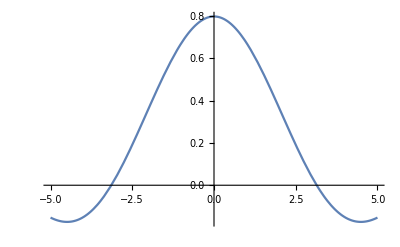

```mathematica
Plot[(√(2/π) Sin[k])/k,{k, -5, 5}, PlotRange->All]
```

```mathematica
FourierTransform[DiracDelta[x-x0], x, k]
```

ⅇ^(ⅈ k x0)/(√(2 π))

-a DiracDelta √(2 π) DiracDelta[k]-ⅈ DiracDelta √(2 π) DiracDelta'[k]

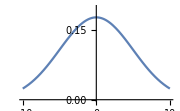

-Graphics-

```mathematica
Plot[F[1], {x, -10, 10} ]
```